```mathematica
SetDirectory[NotebookDirectory[]<>"Simulation/Simulation/bin/Release"];
```

```mathematica
Set[#,"--"<>ToString@#]&/@{
NodeCount,
CouplingRadius,
CouplingStrength,
TimeScale,
DiffusionConstant,
DeltaTime,
WarmupTime,
MeasurementInterval,
MaximumTime,
DelayTime,
Seed,
BifurcationParameterMean,
BifurcationParameterVariance,
SpikeActivationThreshold,
SpikePeakThreshold
};
Set[#,ToString@#]&/@{
Config,
Trajectory,
InterspikeInterval
};
```

```mathematica
LogRange[a_,b_,n_,base_]:=base^Range[a,b,(b-a)/(n-1)];
LogRange[a_,b_,n_]:=LogRange[a,b,n,10];
```

```mathematica
Read2DData[file_,type_]:=Block[{data},
With[{n=BinaryRead[file,"Integer32"]},
data=Table[With[{m=BinaryRead[file,"Integer32"]},
Table[BinaryRead[file,type],{j,m}]
],{i,n}]
];
Close@file;
data];
```

```mathematica
RunCommand[args__]:=RunProcess[{"Simulation.exe",args},"StandardOutput"];
GetConfig[guid_]:=Association@@(#[[1]]->ToExpression[#[[3,1]]]&/@Import["./Data/"<>guid<>"/Config.xml"][[2,3]])
GetTrajectory[guid_]:=Transpose@Read2DData["./Data/"<>guid<>"/Trajectory.bin","Real64"];
GetInterspikeInterval[guid_]:=Read2DData["./Data/"<>guid<>"/ISI.bin","Real64"];
ClearData[guid_]:=DeleteDirectory["./Data/"<>guid,DeleteContents->True];
RunSeries[variable_,values_,fixedArgs__]:=RunCommand[variable,#,fixedArgs]&/@values;
```

```mathematica
PlotTrajectory[guid_]:=With[{traj=GetTrajectory@guid},
ArrayPlot@traj];
PlotInterspikeIntervalPDF[guid_]:=With[{isi=GetInterspikeInterval@guid},
Histogram[Flatten@isi,
PlotLabel->"R = "<>ToString@CalculateSignalToNoiseRatio@guid]];
CalculateSignalToNoiseRatio[guid_]:=With[{isi=Flatten@GetInterspikeInterval@guid},
If[Length@isi>0,
With[{mean=Moment[isi,1],variance=Moment[isi,2]},
Sqrt[variance-mean^2]/mean],-1]];
```

```mathematica
With[{guids=RunSeries[DiffusionConstant,{0.00012,0.001,0.005,0.05},
Seed,42,
BifurcationParameterVariance,0.05,
Config,
Trajectory,
InterspikeInterval]},
With[{result=GraphicsGrid[Transpose@{
PlotTrajectory/@guids,
PlotInterspikeIntervalPDF/@guids},
ImageSize->Large]},
ClearData/@guids;
result]]
```

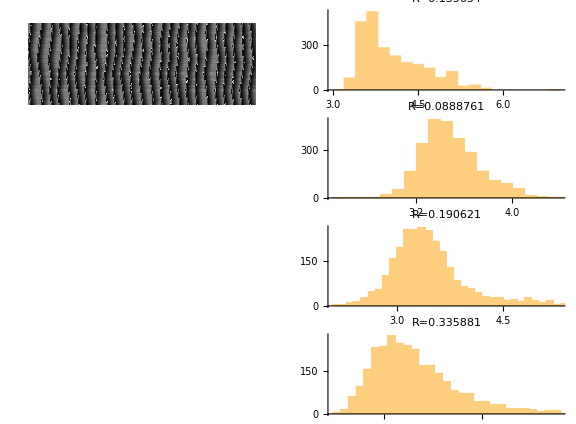

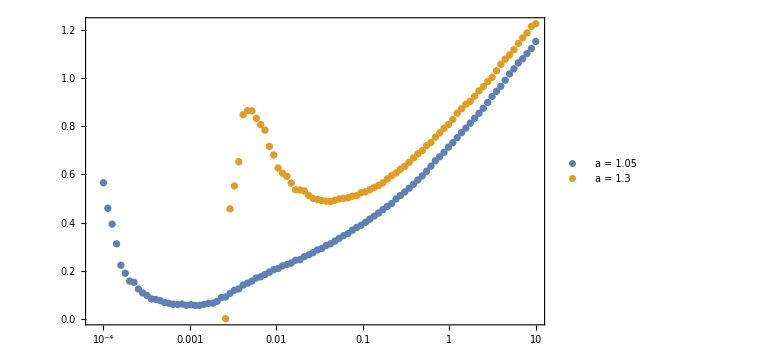

```mathematica
With[{as={1.05,1.3},ds=LogRange[-4.0,1.0,100]},
With[{curves=Table[With[{guids=RunSeries[DiffusionConstant,ds,
Seed,42,
NodeCount,100,
WarmupTime,100,
MaximumTime,500,
BifurcationParameterMean,a,
BifurcationParameterVariance,0,
Config,
InterspikeInterval]},
DeleteCases[MapThread[List,{ds,CalculateSignalToNoiseRatio/@guids}],
{x_,y_}/;y<0]],{a,as}]},
ListLogLinearPlot[curves,
Axes->False,
Frame->True,
PlotLegends->("a = "<>ToString@#&/@as),
ImageSize->Large]]]
```